```mathematica
Clear@@Names@"`*"
$HistoryLength=3;
pwd=NotebookDirectory[];
SetDirectory[pwd];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}","\\usepackage{siunitx}"}]
BeginPackage["PolygonPlotMarkers`"];

ClearAll[PolygonMarker];
PolygonMarker::usage="\!\(\*RowBox[{\"PolygonMarker\", \"[\", RowBox[{StyleBox[\"shape\", \"TI\"], \",\", StyleBox[\"size\", \"TI\"]}], \"]\"}]\) returns Polygon of \!\(\*StyleBox[\"shape\", \"TI\"]\) with centroid at {0,0} and area \!\(\*SuperscriptBox[StyleBox[\"size\", \"TI\"], StyleBox[\"2\", \"TR\"]]\).";
SyntaxInformation[PolygonMarker]={"ArgumentsPattern"->{_,_.,_.}};

Begin["`Private`"];

ClearAll[PolygonArea,PolygonCentroid,LineIntersectionPoint,ngon,nstar,ncross,scale,coords];
(*The shoelace method for computing the area of polygon https://mathematica.stackexchange.com/a/22587/280*)
PolygonArea[pts_?MatrixQ]:=Abs@Total[Det/@Partition[pts,2,1,1]]/2;
(*https://mathematica.stackexchange.com/a/7715/280*)
PolygonCentroid[pts_?MatrixQ]:=With[{dif=Map[Det,Partition[pts,2,1,{1,1}]]},ListConvolve[{{1,1}},Transpose[pts],{-1,-1}].dif/(3 Total[dif])];
(*https://mathematica.stackexchange.com/a/51399/280*)
LineIntersectionPoint[{a_,b_},{c_,d_}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}];

ngon[n_,phase_: 0]:=Table[{0,1}.RotationMatrix[2 k Pi/n+phase],{k,0,n-1}];
(*nn-number of vertices in related polygram step-step at which vertices in the polygram are connected n-number of points in the final star an illustration:http://en.wikipedia.org/wiki/Star_polygon#Simple_isotoxal_star_polygons*)
nstar[n_/;n≥5,phase_: 0]:=nstar[n,2,n,phase];
nstar[nn_,step_,n_,phase_: 0]/;Divisible[nn,n]&&nn/2>step>nn/n:=Module[{a1,a2,b1,b2,ab},{a1,a2,b1,b2}=ngon[nn][[{1,1+step,1+nn/n,nn/n-step}]];
ab=LineIntersectionPoint[{a1,a2},{b1,b2}];
Flatten[Table[{a1,ab}.RotationMatrix[2 k Pi/n+phase],{k,0,n-1}],1]];
(*a-semiwidths of the crossing stripes*)
ncross[n_,phase_: 0,a_: 1/10]:=Flatten[NestList[#.RotationMatrix[2 Pi/n]&,{{-a,1},{a,1},{a,a Cot[Pi/n]}}.RotationMatrix[phase],n-1],1];

(*Unitizes the area of the polygon*)
scale[coords_]:=Chop[#/Sqrt@PolygonArea@#]&@N[coords,{18,18}];

coords["UpTriangle"|"Triangle"]=ngon[3]//scale;
coords["DownTriangle"]=ngon[3,Pi/3]//scale;
coords["LeftTriangle"]=ngon[3,Pi/6]//scale;
coords["RightTriangle"]=ngon[3,-Pi/6]//scale;
coords["ThreePointedStar"]=nstar[12,5,3]//scale;
coords["DiagonalSquare"|"Diamond"]=ngon[4,0]//scale;
coords["Square"]=ngon[4,Pi/4]//scale;
coords["FourPointedStar"]=nstar[8,3,4]//scale;
coords["DiagonalFourPointedStar"]=nstar[8,3,4,Pi/4]//scale;
coords["Pentagon"]=ngon[5]//scale;
coords["FivePointedStar"]=nstar[5]//scale;
coords["FivePointedStarThick"]=nstar[20,7,5]//scale;
coords["Hexagon"]=ngon[6]//scale;
coords["SixPointedStar"]=nstar[6]//scale;
coords["SixPointedStarSlim"]=nstar[12,5,6]//scale;
coords["SevenPointedStar"]=nstar[7]//scale;
coords["SevenPointedStarNeat"]=nstar[14,5,7]//scale;
coords["SevenPointedStarSlim"]=nstar[14,6,7]//scale;
coords["Cross"|"+"]=ncross[4]//scale;
coords["DiagonalCross"|"X"|"x"]=ncross[4,Pi/4]//scale;
coords["TripleCross"|"TripleCrossUp"]=ncross[3]//scale;
coords["TripleCrossDown"|"Y"|"y"]=ncross[3,Pi/3]//scale;
coords["FivefoldCross"]=ncross[5]//scale;
coords["SixfoldCross"]=ncross[6]//scale;
coords["SevenfoldCross"]=ncross[7]//scale;
coords["EightfoldCross"]=ncross[8]//scale;

(*The truncated triangle shape originates from the Cross's Theorem http://demonstrations.wolfram.com/CrosssTheorem/*)
coords["UpTriangleTruncated"|"TriangleTruncated"|"TruncatedTriangle"]=Flatten[{{-3,6+Sqrt[3]},{3,6+Sqrt[3]}}.RotationMatrix[# Pi/3]&/@{0,2,4},1]//scale;
coords["DownTriangleTruncated"]=coords["UpTriangleTruncated"].ReflectionMatrix[{0,1}];
coords["LeftTriangleTruncated"]=coords["UpTriangleTruncated"].RotationMatrix[Pi/6];
coords["RightTriangleTruncated"]=coords["UpTriangleTruncated"].RotationMatrix[-Pi/6];
(*Circle approximated by 24-gon*)
coords["Circle"|"Disk"]=ngon[24]//scale;

(*Plotting symbols recommended in[Cleveland W.S.The Elements of Graphing Data (1985)]*)
(*Symmetric symbol "H"*)
coords["H"]=Join[#,-#]&@Join[#,Reverse@#.{{1,0},{0,-1}}]&@{{333,108},{333,630},{585,630}}//scale;
(*Symmetric symbol "I"*)
coords["I"]=Join[#,-#]&@{{-20,-68},{-64,-68},{-64,-104},{64,-104},{64,-68},{20,-68}}//scale;
(*Antisymmetric symbol "N"*)
coords["N"]=Join[#,-#]&@{{18,-32},{30,-32},{30,32},{17,32},{17,-12}}//scale;
(*Antisymmetric symbol "Z"*)
coords["Z"]=Join[#,-#]&@{{-567,-432},{-567,-630},{567,-630},{567,-414},{-234,-414}}//scale;
(*Antisymmetric symbol "S" (simple)*)
coords["S"]=Join[#,-#]&@{{-176,-54},{116,-54},{167,-100},{167,-170},{116,-216},{-284,-216},{-284,-324},{176,-324},{293,-216},{293,-54}}//scale;
(*Antisymmetric symbol "S" (curved,long)*)
coords["LongS"|"SLong"|"Sl"]=Join[#,-#]&@{{-49/16,-3/11},{-425/91,23/28},{-141/26,31/12},{-165/32,88/19},{-167/45,106/17},{-24/17,149/21},{121/69,233/33},{130/27,31/5},{130/27,118/29},{127/47,199/39},{7/20,233/42},{-12/7,139/26},{-65/21,139/31},{-395/113,114/35},{-157/52,77/39},{-83/44,56/41},{9/22,39/43}}//scale;
(*Antisymmetric symbol "S" curved,wide*)
coords["WideS"|"SWide"|"Sw"]=Join[#,-#]&@{{80/11,-3/5},{49/6,-9/4},{97/12,-41/11},{39/5,-35/8},{88/13,-65/12},{51/10,-49/8},{2,-13/2},{-20/11,-13/2},{-37/8,-81/13},{-81/13,-40/7},{-59/8,-54/11},{-81/10,-26/7},{-70/11,-29/9},{-57/11,-46/11},{-11/4,-33/7},{11/7,-19/4},{16/3,-37/9},{31/5,-38/11},{32/5,-38/13},{37/6,-49/24},{61/13,-6/5},{23/7,-13/14},{-25/9,-4/5},{-23/4,-3/13}}//scale;

PolygonMarker[name_String]:=Polygon[coords[name]];
PolygonMarker[name_String,size_?NumericQ]:=Polygon[size coords[name]];
PolygonMarker[name_String,(h:Scaled|Offset)[size_?NumericQ]]:=Polygon[h[size #,{0,0}]&/@coords[name]];
PolygonMarker[coords:{{_?NumericQ,_?NumericQ}..},size_?NumericQ]:=Polygon[size N[scale[Transpose[Transpose[coords]-PolygonCentroid[coords]]],{16,16}]];
PolygonMarker[coords:{{_?NumericQ,_?NumericQ}..},Scaled[size_?NumericQ]]:=Polygon[Scaled[size #,{0,0}]&/@N[scale[Transpose[Transpose[coords]-PolygonCentroid[coords]]],{16,16}]];
PolygonMarker[arg:_String|{{_?NumericQ,_?NumericQ}..},size:_?NumericQ|(Scaled|Offset)[_?NumericQ],positions:{_?NumericQ,_?NumericQ}|{{_?NumericQ,_?NumericQ}..}]:=Translate[PolygonMarker[arg,size],positions];
(*The list of all available shapes*)
PolygonMarker[]=PolygonMarker[All]={"TripleCross","Y","UpTriangle","UpTriangleTruncated","DownTriangle","DownTriangleTruncated","LeftTriangle","LeftTriangleTruncated","RightTriangle","RightTriangleTruncated","ThreePointedStar","Cross","DiagonalCross","Diamond","Square","FourPointedStar","DiagonalFourPointedStar","FivefoldCross","Pentagon","FivePointedStar","FivePointedStarThick","SixfoldCross","Hexagon","SixPointedStar","SixPointedStarSlim","SevenfoldCross","SevenPointedStar","SevenPointedStarNeat","SevenPointedStarSlim","EightfoldCross","Disk","H","I","N","Z","S","Sw","Sl"};
(*A subset of plot markers suitable for use when plotting symbols on the plot significantly overlap.*)
PolygonMarker["Overlap"]={"TripleCross","Y","UpTriangle","DownTriangle","LeftTriangle","RightTriangle","ThreePointedStar","Cross","DiagonalCross","Diamond","Square","FourPointedStar","DiagonalFourPointedStar","FivefoldCross","FivePointedStar","FivePointedStarThick","Disk","H","I","N","Z","S","Sl"};

End[];

EndPackage[];

em[name_,size_: 7]:=Graphics[{Dynamic@EdgeForm@Directive[CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[2],Opacity[1]],FaceForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}]
emw[name_,size_: 7]:=Graphics[{Dynamic@EdgeForm@Directive[CurrentValue["Color"],JoinForm["Round"],AbsoluteThickness[2],Opacity[1]],FaceForm[White],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}]
fm[name_,size_: 7]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,txfonts},\usepackage{siunitx}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
dat=Import["Harm_zlayer_1.out"];
pnts=dat[[All,{1,2}]];
```

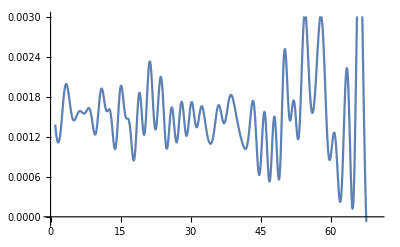

```mathematica
ListPlot[pnts,Joined-> True,InterpolationOrder->10]
```

```mathematica
pnts[[All,2]]=Accumulate[pnts[[All,2]]]
```

{0.00138206,0.00257707,0.00448148,0.00625406,0.00769795,0.00926899,0.0108189,0.0124409,0.0138372,0.0152239,0.0171444,0.0187273,0.0202102,0.0212712,0.0232201,0.0247423,0.0260943,0.0269873,0.0288434,0.0300721,0.032285,0.0339194,0.0355772,0.0374502,0.0384836,0.0401209,0.0412367,0.0429542,0.0441833,0.0458559,0.0472552,0.0488334,0.0503059,0.0514205,0.0526927,0.0543654,0.0557802,0.057453,0.0592324,0.060664,0.0617877,0.0628333,0.064455,0.0657011,0.0664982,0.0679848,0.0685408,0.0700297,0.0706149,0.0730419,0.0746243,0.0763665,0.0775281,0.0801429,0.0827672,0.0843285,0.0865969,0.0895935,0.091198,0.0921092,0.0932796,0.0935035,0.0952361,0.0966392,0.097185,0.101436,0.1034,0.102746,0.100365,0.0947926}

```mathematica
f=BSplineFunction[pnts,SplineDegree->3]
```

BSplineFunction[…]

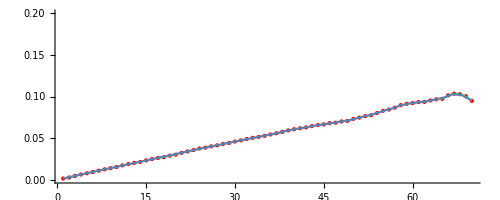

```mathematica
Show[Graphics[{Red,Point[pnts],Green,Line[pnts]},Axes->True],ParametricPlot[f[t],{t,0,70}],PlotRange->{Automatic,{0.0,0.2}}]
```